# Poincare Sphere Coupled Mode Theory Multi- Electrode Directional Coupler with pre and post bias electrodes

## Standard Coupled mode theory definitions:

```mathematica
A1  is defined as the complex coefficient representing the amplitude and phase of  the optical field in  guide "1"
A2  is defined as the complex coefficient representing the amplitude and phase of  the optical field in  guide "2"

From this two mode basis set a basis transformation is made to a symmetric optical eigenmode an antisymmetric optical eigenmode through the following  definition:
```

```mathematica
S2 =. ; S1 =. ; S3 =. ; A1 =. ; A2 =. ; X1 =. ; X2 =. ; X3 =. ; b1 =. ; b2 =. ; b3 =. ; 
dbeta =. ; As =. ; Aa =. ; rr =. ; L1 =. ; L2 =. ; L3 =. ; Signal =. ; tl =. ; xx1 =. ; P11 =. ; rr =. 
prebias=.;postbias=.;
```

```mathematica
(* Define the symetric and antisymetric wave equations*)
 Aso=(A1+A2)/(√2);
Aao= (A1-A2)/(√2);
```

Initial Conditions 
Dc Pre-Bias E1 =  √(dbeta^2/4+1/49 dbeta^2 π^2 prebias^2)
Drive Voltage Center Electrode = √(dbeta^2/4+dbeta^2 (0.4+Signal)^2)
 Post-Bias E3 = √(dbeta^2/4+dbeta^2 postbias^2)

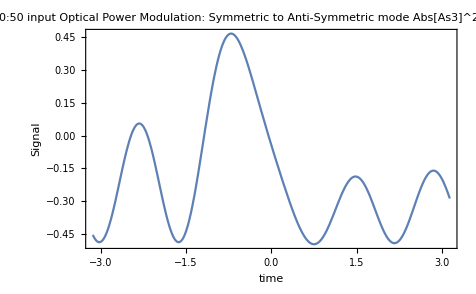

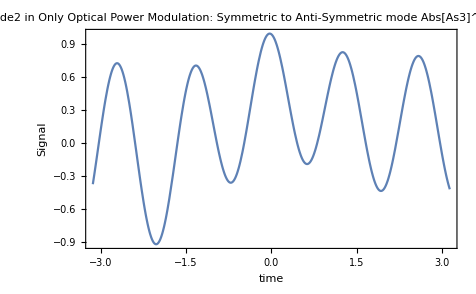

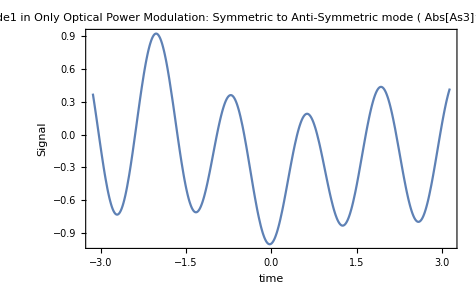

```mathematica
(*Initial electrode relative length *)
L1=rr*(Pi/dbeta);L2=.75*(Pi/dbeta);L3=rr*(Pi/dbeta);
(* Effective χ_n(Vapplied) *)
X1=  dbeta*( Pi/7 )*prebias;X2=dbeta*(Signal +.4);X3=-dbeta * postbias;

b1=Sqrt[dbeta^2/4+X1^2];
b2=Sqrt[dbeta^2/4+X2^2];
b3=Sqrt[dbeta^2/4+X3^2];
Print["Initial Conditions \nDc Pre-Bias E1 = "b1,"\n","Drive Voltage Center Electrode = ",b2,"\n Post-Bias E3 = ",b3]
(*normalize Delta Beta to 1 *)
dbeta=1;
rr:=.55;

As1=Aso*Cos[b1 L1 ] + ((Aso* dbeta)/(2b1) + (Aao X1/b1))*I Sin[b1 L1];
Aa1=Aao*Cos[b1 L1 ] - ((Aao* dbeta)/(2b1 )- (Aso X1/b1))*I Sin[b1 L1];

As2=As1*Cos[b2 L2] + ((As1* dbeta)/(2b2) + (Aa1 X2/b2))*I Sin[b2 L2];
Aa2=Aa1*Cos[b2 L2 ] - ((Aa1* dbeta)/(2b2 )- (As1 X2/b2))*I Sin[b2 L2];

As3=As2*Cos[b3 L3 ] + ((As2* dbeta)/(2b3) + (Aa2 X3/b3))*I Sin[b3 L3];
Aa3=Aa2*Cos[b3 L3 ] - ((Aa2* dbeta)/(2b3)- (As2 X3/b3))*I Sin[b3 L3];


S1[Signal_ ,prebias_,postbias_]:=Evaluate[ Abs[As3]^2-Abs[Aa3]^2];
S2[Signal_ ,prebias_,postbias_  ]:= Evaluate[2*Abs[As3*Aa3] Cos[Arg[As3]-Arg[Aa3]]];
S3[Signal_ ,prebias_,postbias_]:= Evaluate[ 2*Abs[As3*Aa3]Sin[Arg[As3]-Arg[Aa3]]];
(*Inital Waveguide mode*)
A1:=.5;A2:=.5
prebias:=1;postbias:=1;
Plot[S1[Signal,prebias,postbias],{Signal,-Pi,Pi},Frame->True, FrameLabel->{"time","Signal"},PlotLabel->"50:50 input Optical Power Modulation: Symmetric to Anti-Symmetric  mode
 Abs[As3]^2-Abs[Aa3]^2"]

A1:=0;A2:=1;
prebias:=1;postbias:=1;
Plot[S1[Signal,prebias,postbias],{Signal,-Pi,Pi},Frame->True, FrameLabel->{"time","Signal"},PlotLabel->"Guide2 in Only Optical Power Modulation: Symmetric to Anti-Symmetric  mode
  Abs[As3]^2-Abs[Aa3]^2]"]
A1:=1;A2:=0;
prebias:=1;postbias:=1;
Plot[S1[Signal,prebias,postbias],{Signal,-Pi,Pi},Frame->True, FrameLabel->{"time","Signal"},PlotLabel->"Guide1 in Only Optical Power Modulation: Symmetric to Anti-Symmetric  mode
 ( Abs[As3]^2-Abs[Aa3]^2)"]
```

## Optical Power Output Waveguide

1/2+0.499067 Abs[1/(0.41+0.8 sig+sig^2)(1. √(0.41+0.8 sig+sig^2) Cos[2.35619 √(0.41+0.8 sig+sig^2)]+((-0.0790788+0.0370458 ⅈ)-(0.758488-0.672999 ⅈ) sig) Sin[2.35619 √(0.41+0.8 sig+sig^2)]) (1. √(0.41+0.8 sig+sig^2) Cos[2.35619 √(0.41+0.8 sig+sig^2)]+((0.0699781-0.872451 ⅈ)+(0.671197-0.724232 ⅈ) sig) Sin[2.35619 √(0.41+0.8 sig+sig^2)])] Cos[Arg[(0.524061-0.441398 ⅈ) Cos[2.35619 √(0.41+0.8 sig+sig^2)]+(((-0.0250902+0.0543195 ⅈ)-(0.100433-0.687487 ⅈ) sig) Sin[2.35619 √(0.41+0.8 sig+sig^2)])/(√(0.41+0.8 sig+sig^2))]-Arg[(0.646132+0.336216 ⅈ) Cos[2.35619 √(0.41+0.8 sig+sig^2)]+(((0.338547-0.540191 ⅈ)+(0.67718-0.242283 ⅈ) sig) Sin[2.35619 √(0.41+0.8 sig+sig^2)])/(√(0.41+0.8 sig+sig^2))]]

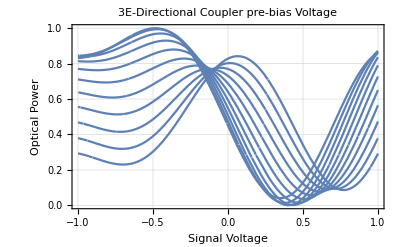

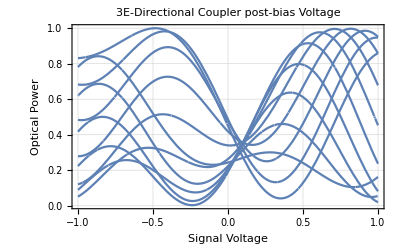

```mathematica
A1:=0;A2:=1;

preb=.
postb=.
P11[signal_,preb_,postb_]:=Evaluate[( 1+S2[signal,preb,postb])/2];
P22[signal_,preb_,postb_]:=Evaluate[( 1-S2[signal,preb,postb])/2];
preb:=1
postb:=1
Simplify[P11[sig,preb,postb]]
prebMax=1;
prebMin=-1;
postbMax=prebMax;
postbMin=prebMin;
biastable1:=Table[Plot[Evaluate[P11[signal,preb,postb]],{signal,-1,1},PlotRange->All,Frame->True,PlotLabel->"3E-Directional Coupler pre-bias Voltage",GridLines->Automatic,FrameLabel->{"Signal Voltage","Optical Power "}],{preb,prebMin,prebMax,.2}]
Show[Table[biastable1[[zzz]],{zzz,1,Length[biastable1]}]]
biastable1:=Table[Plot[Evaluate[P11[signal,preb,postb]],{signal,-1,1},PlotRange->All,Frame->True,PlotLabel->"3E-Directional Coupler post-bias Voltage",GridLines->Automatic,FrameLabel->{"Signal Voltage","Optical Power"}],{postb,postbMin,postbMax,.2}]
Show[Table[biastable1[[zzz]],{zzz,1,Length[biastable1]}]]
```

```mathematica
A1:=1;A2:=0;

preb=.
postb=.
P11[signal_,preb_,postb_]:=Evaluate[( 1+S2[signal,preb,postb])/2];
P22[signal_,preb_,postb_]:=Evaluate[( 1-S2[signal,preb,postb])/2];
preb:=1
postb:=1
Simplify[P11[sig,preb,postb]]
```

1/2+0.499067 Abs[1/(0.41+0.8 sig+sig^2)(1. √(0.41+0.8 sig+sig^2) Cos[2.35619 √(0.41+0.8 sig+sig^2)]+((-0.0790788-0.0370458 ⅈ)-(0.758488+0.672999 ⅈ) sig) Sin[2.35619 √(0.41+0.8 sig+sig^2)]) (1. √(0.41+0.8 sig+sig^2) Cos[2.35619 √(0.41+0.8 sig+sig^2)]+((0.0699781+0.872451 ⅈ)+(0.671197+0.724232 ⅈ) sig) Sin[2.35619 √(0.41+0.8 sig+sig^2)])] Cos[Arg[(-0.524061-0.441398 ⅈ) Cos[2.35619 √(0.41+0.8 sig+sig^2)]+(((0.0250902+0.0543195 ⅈ)+(0.100433+0.687487 ⅈ) sig) Sin[2.35619 √(0.41+0.8 sig+sig^2)])/(√(0.41+0.8 sig+sig^2))]-Arg[(0.646132-0.336216 ⅈ) Cos[2.35619 √(0.41+0.8 sig+sig^2)]+(((0.338547+0.540191 ⅈ)+(0.67718+0.242283 ⅈ) sig) Sin[2.35619 √(0.41+0.8 sig+sig^2)])/(√(0.41+0.8 sig+sig^2))]]

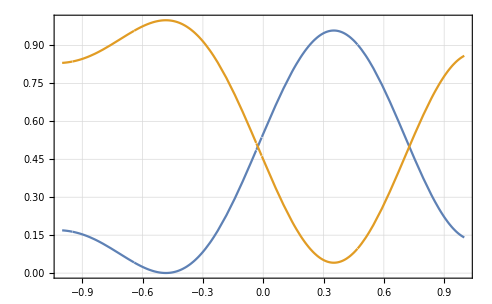

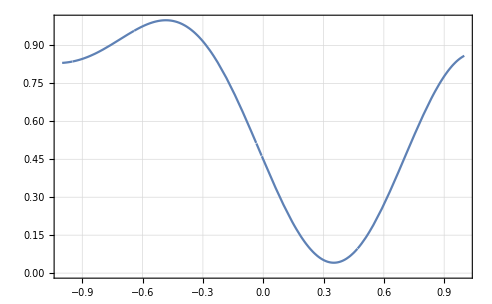

11

```mathematica
Plot[{P11[sig,preb,postb],P22[sig,preb,postb]},{sig,-1,1},Frame->True,GridLines->Automatic]
Plot[P22[sig,preb,postb],{sig,-1,1},Frame->True,GridLines->Automatic]
Print[preb,postb]
```

```mathematica
Plot3D[P11[signal,0,1],{signal,-2, 2},PlotPoints->50,FaceGrids->All, PlotLabel-> "Single Electrode Directional Coupler Modulator Response",
AxesLabel->{"Device Length (coupling length)","Switching Voltage (Vpi)","Optical Power (Normalized)"}]
```

⁃SurfaceGraphics⁃

Two parameters of the directional coupler modulator are coupling length, (tl) ,and the strength of the coupling factor between the two optical guides as a function of the applied voltage, S2[voltage applied]. The following three dimensional plot shows the Optical power in guide one as function of these two variables:

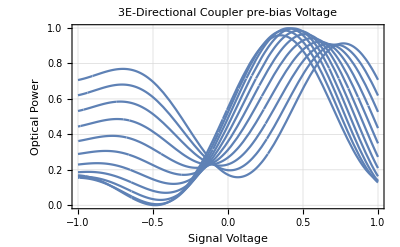

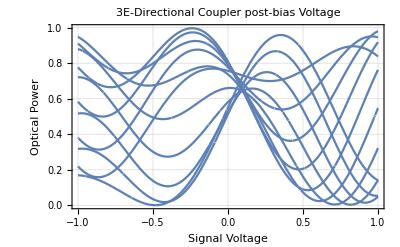

```mathematica
prebMax=1;
prebMin=-1;
postbMax=prebMax;
postbMin=prebMin;
biastable1:=Table[Plot[Evaluate[P11[signal,preb,postb]],{signal,-1,1},PlotRange->All,Frame->True,PlotLabel→
 "3E-Directional Coupler pre-bias Voltage",GridLines->Automatic,
 FrameLabel->{"Signal Voltage","Optical Power "}],{preb,prebMin,prebMax,.2}]
Show[Table[biastable1[[zzz]],{zzz,1,Length[biastable1]}]]
biastable1:=Table[Plot[Evaluate[P11[signal,preb,postb]],{signal,-1,1},PlotRange->All,Frame->True,PlotLabel→
 "3E-Directional Coupler post-bias Voltage",
 GridLines->Automatic,
 FrameLabel->{"Signal Voltage","Optical Power"}],{postb,postbMin,postbMax,.2}]
Show[Table[biastable1[[zzz]],{zzz,1,Length[biastable1]}]]
```

Fixing the coupling length (tl)  such that with zero bias or drive voltage all of the optical power is transferred to the other optical waveguide;
 Delta beta * length =Pi 
 
Then the with initial bias points, signal is applied to the central electrode

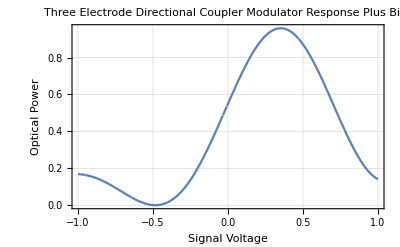

```mathematica
tl:=1
preb:=1
Plot[P11[signal,1,1],{signal ,-1,1},PlotRange->All,Frame->True,
PlotLabel→ "Three Electrode Directional Coupler Modulator Response Plus Bias",
FrameLabel->{"Signal Voltage","Optical Power "},GridLines->Automatic]
```